```mathematica
Clear[a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,y1,y2,y3,dy,dz,diffz,diz,z,eq]
```

```mathematica
Solve[r^2-2r+5==0]
```

{{r→1-2 ⅈ},{r→1+2 ⅈ}}

```mathematica
a[t_]:=E^t(Cos[2t]+I*Sin[2t])
a[t]
a[Pi/2]
da[t_]=D[a[t],t]
da[Pi/2]
```

ⅇ^t (Cos[2 t]+ⅈ Sin[2 t])

-ⅇ^(π/2)

ⅇ^t (2 ⅈ Cos[2 t]-2 Sin[2 t])+ⅇ^t (Cos[2 t]+ⅈ Sin[2 t])

(-1-2 ⅈ) ⅇ^(π/2)

```mathematica
b[t_]:=E^t(Cos[-2t]+I*Sin[-2t])
b[t]
b[Pi/2]
db[t_]=D[b[t],t]
db[Pi/2]
```

ⅇ^t (Cos[2 t]-ⅈ Sin[2 t])

-ⅇ^(π/2)

ⅇ^t (-2 ⅈ Cos[2 t]-2 Sin[2 t])+ⅇ^t (Cos[2 t]-ⅈ Sin[2 t])

(-1+2 ⅈ) ⅇ^(π/2)

```mathematica
m=MatrixForm[RowReduce[{{Out[614],Out[619],0},{Out[616],Out[621],2}}]]
```

(1 | 0 | 1/2 ⅈ ⅇ^(-π/2)
0 | 1 | -1/2 ⅈ ⅇ^(-π/2))

```mathematica
c1=m[[1]][[1]][[3]]
c2=m[[1]][[2]][[3]]
```

1/2 ⅈ ⅇ^(-π/2)

-1/2 ⅈ ⅇ^(-π/2)

```mathematica
y[x_]=Simplify[c1*a[x]+c2*b[x]]
```

-2 ⅇ^(-π/2+x) Cos[x] Sin[x]

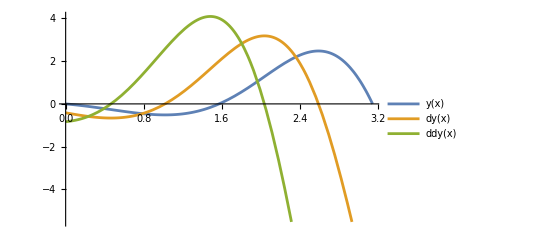

```mathematica
Plot[{y[x],dy[x],ddy[x]},{x,0,Pi},PlotLegends->"Expressions"]
```

```mathematica
y[Pi/2]
```

0

```mathematica
dy[x_]=D[y[x],x]
dy[Pi/2]
```

-2 ⅇ^(-π/2+x) Cos[x]^2-2 ⅇ^(-π/2+x) Cos[x] Sin[x]+2 ⅇ^(-π/2+x) Sin[x]^2

2

```mathematica
ddy[x_]=D[y[x],{x,2}]
```

6 ⅇ^(-π/2+x) Cos[x] Sin[x]-4 ⅇ^(-π/2+x) (Cos[x]^2-Sin[x]^2)

```mathematica
Simplify[ddy[x]-2dy[x]+5y[x]]
```

0

```mathematica
a1=(8-4I)*(-I-Sqrt[3])
```

(8-4 ⅈ) (-ⅈ-√3)

```mathematica
b1=Re[a1/4]+I*Im[a1/4]
```

-1-2 √3+ⅈ (-2+√3)

```mathematica
a2=(2+I)(-I+Sqrt[3])
```

(2+ⅈ) (-ⅈ+√3)

```mathematica
b2=Re[a2]+I*Im[a2]
```

1+2 √3+ⅈ (-2+√3)

```mathematica
Simplify[b1*a[t]+b2*b[t]]
```

2 ⅈ ((-2+√3) Cos[t]-(1+2 √3) Sin[t])

```mathematica
DSolve[y''[x]-2y'[x]+5y[x]==0,y[x],x]
```

{{y[x]→ⅇ^x C[2] Cos[2 x]+ⅇ^x C[1] Sin[2 x]}}

```mathematica
y[x_]:=(E^(x))(a*Cos[2*x]+b*Cos[2*x])
```

```mathematica
Simplify[y[x]]
```

(a+b) ⅇ^x Cos[2 x]

```mathematica
Simplify[y[Pi/2]==0]
```

a+b==0

```mathematica
dy[x_]=Simplify[D[Simplify[y[x]],x]]
Simplify[dy[Pi/2]==2]
```

(a+b) ⅇ^x (Cos[2 x]-2 Sin[2 x])

-((a+b) ⅇ^(π/2))==2

```mathematica
D[E^x*Cos[2x],x]
```

ⅇ^x Cos[2 x]-2 ⅇ^x Sin[2 x]